```mathematica
Lecture 9: Single Variable Calculus
```

Key calculus functions include:

```mathematica
{Limit,D,Integrate,NIntegrate,FindRoot,Solve,Series,Normal,Maximize,NMaximize,Evaluate,ArcLength}
```

## Limits

### Exercise Subsection

Use known Calculus theorems and definitions to predict the output of the following cells:

```mathematica
Clear[f,x,a,c]
Limit[(f[x+h]-f[x])/h,h->0,Analytic->True]
```

f'[x]

```mathematica
Limit[(f[x]-f[a])/(x-a),x->a,Analytic->True]
```

f'[a]

```mathematica
Limit[c f[x],x->a,Analytic->True]==c Limit[f[x],x->a,Analytic->True]
```

True

### Exercise Subsection

A sequence a[n]where n is a positive integer is defined in the next cell.

```mathematica
a[n_]:=n! ⅇ^n n^(-n-1/2)
```

Create a graphic that shows the ListPlot to plot the first 1000 values of this sequence along with a line depicting its limit at Infinity.

```mathematica
Limit[a[n],n->Infinity]
```

√(2 π)

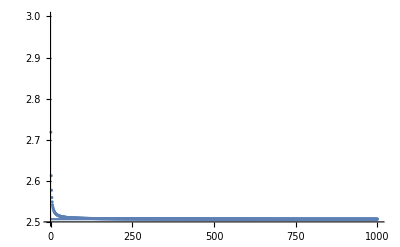

```mathematica
Show[ListPlot[a/@Range@1000,PlotRange->{2.5,3}],Plot[Sqrt[2 Pi],{x,0,1000}]]
```

### Exercise Subsection

Plot the function defined in the next cell and then create a graphic showing the plot of the function together with its limit at Infinity.

```mathematica
f[x_]:=(ⅇ^x x+Sin[x]+Cos[x] Sinh[x])/(ⅇ^x x+Sin[x])
```

### Exercise Subsection

a. Produce a graphic that shows the ParametricPlot of the circle described by the parametric equations {Cos[t],Sin[t]} together with the inscribed polygon created by connecting 12 equally spaced points on the circle.

```mathematica
G1=ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}];
```

```mathematica
G2=Graphics[{Orange,Line@Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/6}]}];
```

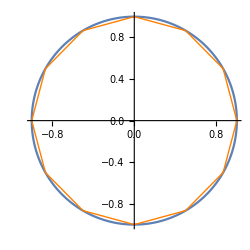

```mathematica
Show[G1,G2]
```

b. Use ArcLength to find the arc length of the inscribed polygon, thereby approximating the value of 2 Pi.

```mathematica
ArcLength@Line@Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/100}]//N
```

6.28293

```mathematica
2Pi//N
```

6.28319

## Derivatives

### Exercise Subsection

Define a function PlotTangentLine[f_, a_] that has input a differentiable function f of one variable and real number a and output the plot of f together with the line tangent to f at a on the interval from a-1 to a+1.

```mathematica
f[x_]:=x^2
```

```mathematica
f'[x]
```

2 x

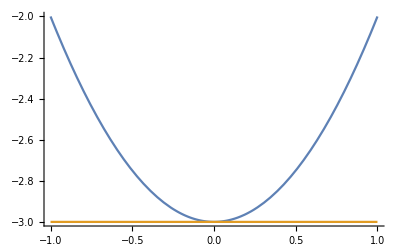

```mathematica
PlotTangentLine[f_,a_]:=Plot[{f[x],(x-a) f'[a] + f[a]},{x,a-1,a+1}]
g[x_]:=x^2-3
PlotTangentLine[g,0]
```

### Exercise Subsection

Find the maximum value of the function x^(a/x) where both x and a are positive.

### Exercise Subsection

The mean value theorem says that if f[x] is differentiable for values of x between a and b, then there a point c strictly between a and b such that f’[c]=(f[b]-f[a])/(b-a).

a. Let f[x] be the function defined in the next cell.  Find one such value of c in the mean value theorem (consider selecting one of the the real elements of NSolve that is in the correct interval) when taking a to be the number that minimizes f[x] (consider Minimize) and b is the number that maximizes f[x] (consider Maximize).

```mathematica
f[x_]:=(x+1)/(2+x^2)
```

b. Plot the following on the same graphic to illustrate the geometric meaning of the mean value theorem. 
1. The Plot of f[x] on the interval from a to b.
2. A Point at each of {a,f[a]}, {b,f[b]}, {c,f[c]}.
3. The InfiniteLine passing through the points {a,f[a]} and {b,f[b]}.
4. The InfiniteLine tangent to f[x] at x=c.

## Integrals

### Exercise Subsection

Use known Calculus theorems and definitions to predict the output of the following cells:

```mathematica
Clear[f]
```

```mathematica
D[∫_a^t f[x]ⅆx,t]
```

f[t]

```mathematica
∫D[f[x],x]ⅆx
```

f[x]

### Exercise Subsection

Let f[x_,σ_,μ_] be the function defined in the next cell:

```mathematica
f[x_,σ_,μ_]:=1/(σ √(2 π))Exp[-(x-μ)^2/(2 σ^2)]
```

a. Use Manipulate to Plot the function f as a function of x where σ can take values between 1/4 and 4 and μ values between -4 and 4. Be sure to set PlotRange and any other Plot options to best illustrate the situation.

```mathematica
Manipulate[Plot[f[x,σ,μ],{x,-4,4},PlotRange->{0,3}],{σ,1/4,4},{μ,-4,4}]
```

b. Find all critical points (where the derivative is equal to 0) and all inflection points (where the second derivative is 0) for f as a function of x.  Consider using Reduce as an alternative to Solve.

```mathematica
Solve[D[f[x,σ,μ],{x,2}]==0,x]//Quiet
```

{{x→μ-σ},{x→μ+σ}}

```mathematica
Reduce[D[f[x,σ,μ],{x,2}]==0,x]
```

σ≠0&&(x==μ+σ||x==μ-σ)

c. Simplify the Integral of f with respect to x on the interval from 0 to ∞, both without any assumptions and then with the Simplify assumptions of And[Element[σ,Reals],σ >0,μ==0].

```mathematica
Simplify[Integrate[f[x,σ,μ],{x,0,∞}],σ>0]
```

1/2 (1+Erf[μ/(√2 σ)])

### Exercise Subsection

The this integral is from the final round of the 2023 MIT integration bee:

```mathematica
Integrate[Tan[x]^(1/3)/(Cos[x]+Sin[x])^2,x]
```

Evaluate the integral and then use FunctionSingularities to describe the values of x for which the resulting function is not defined (where the function has a division by 0 singularity).

### Exercise Subsection

The average value of a function f[x] on the interval from a to b is given by Integrate[f[x],{x,a,b}]/(b-a).  Find a value of t such that the average value of the function Exp[-x] Sin[x] on the interval from 0 to t is equal to 1 (consider FindRoot).

### Exercise Subsection

The probabilist's Hermite polynomials are a sequence of polynomials defined by the recursion H[0,x] is equal to 1 and H[n,x] is equal to x H[n-1,x] - D[H[n-1,x],x] otherwise.

a. What is the 50th Hermite polynomial?  (Use Expand in the definition of the recursion together with memoization to get better results.)

b. Create a 8x8 matrix with i,j entry equal to ∫_(-∞)^∞ 1/(√(2 π))Exp[-x^2/2]*H[i,x]*H[j,x]ⅆx and then make a conjecture about what the entries of the corresponding nxn matrix would be.

```mathematica
H[n_,x_]:=H[n,x]=Expand@If[n==0,1,x H[n-1,x] - D[H[n-1,x],x]]
```

```mathematica
Table[H[n,x],{n,0,10}]
```

{1,x,-1+x^2,-3 x+x^3,3-6 x^2+x^4,15 x-10 x^3+x^5,-15+45 x^2-15 x^4+x^6,-105 x+105 x^3-21 x^5+x^7,105-420 x^2+210 x^4-28 x^6+x^8,945 x-1260 x^3+378 x^5-36 x^7+x^9,-945+4725 x^2-3150 x^4+630 x^6-45 x^8+x^10}

```mathematica
Table[∫_(-∞)^∞ 1/(√(2 π))Exp[-x^2/2]*H[i,x]*H[j,x]ⅆx,{i,8},{j,8}]
```

{{1,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,0},{0,0,6,0,0,0,0,0},{0,0,0,24,0,0,0,0},{0,0,0,0,120,0,0,0},{0,0,0,0,0,720,0,0},{0,0,0,0,0,0,5040,0},{0,0,0,0,0,0,0,40320}}

```mathematica
%//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 24 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 120 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 720 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 5040 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 40320)

## Series

### Exercise Subsection

Show that the first 100 terms in the series for Exp[I x] is equal to the first 100 terms in the series for Cos[x] + I Sin[x].

```mathematica
Series[Exp[I x],{x,0,10}]
```

1+ⅈ x-x^2/2-(ⅈ x^3)/6+x^4/24+(ⅈ x^5)/120-x^6/720-(ⅈ x^7)/5040+x^8/40320+(ⅈ x^9)/362880-x^10/3628800+O[x]^11

```mathematica
Series[Cos[x] + I Sin[x],{x,0,10}]
```

1+ⅈ x-x^2/2-(ⅈ x^3)/6+x^4/24+(ⅈ x^5)/120-x^6/720-(ⅈ x^7)/5040+x^8/40320+(ⅈ x^9)/362880-x^10/3628800+O[x]^11

### Exercise Subsection

a. Use ListAnimate to show the Plot of of the function 1/(1-x) on the interval from -4 to 4 together with the degree n polynomial Series[1/(1-x),{x,0,n}] as n ranges from 0 to 25.

b. Redo part a. two more times, once when taking -1 as the center of the series instead of 0, and once when taking 1/2 as the center of the series.

```mathematica
ListAnimate@Table[Show[Plot[1/(1-x),{x,-4,4}],
Plot[Evaluate@Normal@Series[1/(1-x),{x,-2,n}],{x,-4,4}]],{n,0,25}]
```

```mathematica
Normal@Series[1/(1-x),{x,0,4}]
```

1+x+x^2+x^3+x^4

### Exercise Subsection

Use SumConvergence to determine the values of x for which these sum converge:

```mathematica
∑_(n=0)^∞ Log[Log[n]]^-x/(n Log[n])
```

```mathematica
SumConvergence[Log[Log[n]]^-x/(n Log[n]),n]
```

x>1

```mathematica
SumConvergence[1/n,n]
```

False

```mathematica
1/2+1/3+1/5+1/7+1/11+1/13+1/17+...
```

### Exercise Subsection

A twin prime is a prime p such that either p-2 or p+2 is also prime.  It is known that the sum of terms of the form 1/p where p is a twin prime converges.  Approximate this sum by selecting the twin primes from the first 10^6 primes and summing the reciprocals.

```mathematica
Plus@@(1/Select[Prime/@Range[10^6],PrimeQ[#-2]||PrimeQ[#+2]&])//N
```

1.54268

```mathematica
Sum[1/p,{p,Select[Prime/@Range[10^6],PrimeQ[#-2]||PrimeQ[#+2]&]}]
```

```mathematica
%//N
```

1.54268